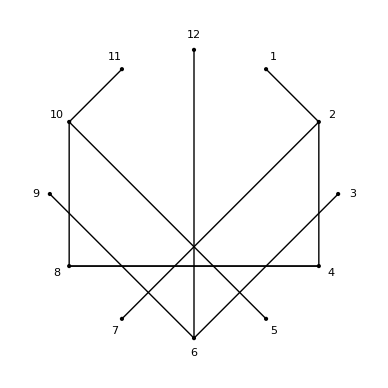

```mathematica
n=12;
m=2;
f[x_]:=m*x;
Graphics[{Rotate[{Point[Table[ReIm[ⅇ^(2*ⅈ*π*j/n)],{j,1,n}]],Table[{"Hue[j/n],";Line[{ReIm[ⅇ^(2*ⅈ*π*j/n)],ReIm[ⅇ^(2*ⅈ*π*f[j]/n)]}]},{j,1,n}]},90°,{0,0}],Table[Text[j,1.1*ReIm[ⅇ^(-2*ⅈ*π*j/n+ⅈ*π/2)]],{j,1,n}]}]
```

```mathematica
n=100;
Manipulate[Graphics[{Rotate[{Point[Table[ReIm[ⅇ^(2*ⅈ*π*j/n)],{j,1,n}]],Table[Line[{ReIm[ⅇ^(2*ⅈ*π*j/n)],ReIm[ⅇ^(2*ⅈ*π*j*m/n)]}],{j,1,n}]},90°,{0,0}]}],{m,1,n,1}]
```